## MONADS

This Mathematica notebook is licensed under a  
It creates the demonstrations used in my post Monads for High School II.

I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

## Presentation

```mathematica
basesty[list_]:=Framed[Style[list,Medium, 12, FontFamily->"Arial",Background->White]]
```

```mathematica
basesty[Grid[{{1,22,134}}]]
```

1 | 22 | 134

```mathematica
test1=basesty[Grid[{{1,22,134}}]]
```

1 | 22 | 134

```mathematica
cartouche[list_]:=basesty[Grid[{list}]]
```

```mathematica
cartouche[{3,5,7}]
```

3 | 5 | 7

```mathematica
listcar[list_,place_]:=Text[cartouche[list],place]
```

```mathematica
listcar[{4,66,232,5},{2,2}]
```

Text[4 | 66 | 232 | 5,{2,2}]

```mathematica
f[x_]:=Graphics[Text[{{x, 66, 232, 5}},{2,2}]];f[5]
```

-Graphics-

### Thick style

```mathematica
thicksty[list_]:=Style[Grid[{list},Frame->True,FrameStyle->Directive[Thick]],Bold, 12, FontFamily->"Arial",Background->White]
```

```mathematica
thicksty[{1,22,134}]
```

1 | 22 | 134

```mathematica
testthick2=thicksty[{1,22,134}]
```

1 | 22 | 134

```mathematica
testthick3=thicksty[{5,7,2,2,2,2,2,2,2}]
```

5 | 7 | 2 | 2 | 2 | 2 | 2 | 2 | 2

```mathematica
listthicky[list_,place_]:=Text[thicksty[list],place]
```

## Joining lists

### Illustrations of joining lists

#### DONT KILL THIS

```mathematica
Manipulate[
Graphics[
If[d<.675,
{
listcar[{2,12,7},{d,0}],
listcar[{5,7},{2-d,0}]
},
{
listcar[{2,12,7,5,7},{.93,0}]
}
],
PlotRange->{{-.5,2.5},{-.2,.2}},
ImageSize->200,
AspectRatio->Automatic
],
{{d,.6,""},.6,.77},
ControlPlacement->Bottom,
Paneled->False,SaveDefinitions->True
]
```

#### THIS WORKS

```mathematica
Manipulate[
If[b,
DynamicModule[{d=.63},
Dynamic[
(If[d<.68,(d=d+.005;d)];
Graphics[
If[d<.675,
{listcar[{2,12,7},{d,0}],
listcar[{5,7},{2-d,0}]},
{listcar[{2,12,7,5,7},{.93,0}]}
],
PlotRange->{{-.5,2.5},{-.2,.2}},
ImageSize->200
]
)
]
],
Graphics[
{listcar[{2,12,7},{.63,0}],
listcar[{5,7},{2-.63,0}]},PlotRange->{{-.5,2.5},{-.2,.2}},
ImageSize->200, AspectRatio->Automatic
]
],{{b,False,"Join"},{True,False},ControlType->RadioButtonBar},
Paneled->False,SaveDefinitions->True
]
```

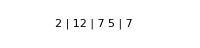

```mathematica
Graphics[
{listcar[{2,12,7},{.63,0}],
listcar[{5,7},{2-.63,0}]},PlotRange->{{-.5,2.5},{-.2,.2}},
ImageSize->200, AspectRatio->Automatic
]
```

#### Working version of “Join”

```mathematica
Manipulate[
If[b=="Join",
DynamicModule[{d=.63},
Dynamic[
(If[d<.68,(d=d+.005;d)];
Graphics[
If[d<.675,
{listcar[{2,12,7},{d,0}],
listcar[{5,7},{2-d,0}]},
{listcar[{2,12,7,5,7},{.93,0}]}
],
PlotRange->{{-.5,2.5},{-.2,.2}},
ImageSize->200
]
)
]
],
Graphics[
{listcar[{2,12,7},{.63,0}],
listcar[{5,7},{2-.63,0}]},PlotRange->{{-.5,2.5},{-.2,.2}},
ImageSize->200, AspectRatio->Automatic
]
],{{b,"Reset",""},{"Join","Reset"}},
Paneled->False,ControlPlacement->Left,SaveDefinitions->True
]
```

### This is join1.cdf

<script type="text/javascript" src="http://www.wolfram.com/cdf-player/plugin/v2.1/cdfplugin.js"></script>
<script type="text/javascript">
var cdf = new cdfplugin();
cdf.setDefaultContent('<a href="http://www.wolfram.com/cdf-player/"><img  src="Join1.png"></a>');
cdf.embed('www.abstractmath.org/Mathematica/Join1.cdf', 305, 66);
</script>

```mathematica
Manipulate[
If[b=="Join",
DynamicModule[{d=.63},
Dynamic[
(If[d<.68,(d=d+.005;d)];
Graphics[
If[d<.675,
{listcar[{2,12,7},{d,0}],
listcar[{5,7},{2-d,0}]},
{listcar[{2,12,7,5,7},{.93,0}]}
],
PlotRange->{{-.5,2.5},{-.2,.2}},
ImageSize->200
]
)
]
],
Graphics[
{listcar[{2,12,7},{.63,0}],
listcar[{5,7},{2-.63,0}]},PlotRange->{{-.5,2.5},{-.2,.2}},
ImageSize->200, AspectRatio->Automatic
]
],{{b,"Reset",""},{"Join","Reset"}},
Paneled->False,ControlPlacement->Left,SaveDefinitions->True
]
```

### Join2

```mathematica
op[x_,loc_]:=Text[Style[x,13,Bold,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op[x_,loc_,weight_]:=Text[Style[x,13,weight,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op[x_,loc_,weight_,color_]:=Text[Style[x,13,weight,color,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
edge[loc1_,loc2_,sf_]:=Arrow[{loc1,loc2},Scaled[sf]]
```

```mathematica
spd=.0009
```

0.0009

```mathematica
cartouche[{2,12,7}]
```

2 | 12 | 7

```mathematica
Remove[uu]
```

```mathematica
uu=cartouche[{2,12,7}]
```

2 | 12 | 7

## The operation Join

### This is Joinex1.cdf

<script type="text/javascript" src="http://www.wolfram.com/cdf-player/plugin/v2.1/cdfplugin.js"></script>
<script type="text/javascript">
var cdf = new cdfplugin();
cdf.setDefaultContent('<a href="http://www.wolfram.com/cdf-player/"><img  src="join1.png"></a>');
cdf.embed('http://www.abstractmath.org/Mathematica/join1.cdf', 258, 149);
</script>

```mathematica
ss=0;If [ss>0,uu,"join"]
```

join

```mathematica
"join"
```

join

```mathematica
joinex:=Manipulate[Graphics[{
Arrowheads[0],
op[If [s>0,cartouche[{2,12,7,5,7}],Text[Framed[Style["join",FontFamily->"Arial"]]]],{-1/2,2}],
op[cartouche[{2,12,7}],{-1,1}],
op[cartouche[{5,7}],{0,1}],
edge[{-1/2,2},{-1,1},.0005],
edge[{-1/2,2},{0,1},.0005]},
Background->White,ImageSize->120, AspectRatio->1],{{s,0,""},{0->"Reset",1->"Evaluate"}},Paneled->False,ControlPlacement->Left,SaveDefinitions->True]
```

```mathematica
joinex
```

### Join is associative

```mathematica
li1=cartouche[{2,12,7}]
```

2 | 12 | 7

```mathematica
li2=cartouche[{5,7}]
```

5 | 7

```mathematica
li3=cartouche[{7,9,8}]
```

7 | 9 | 8

```mathematica
li12=cartouche[{2,12,7,5,7}]
```

2 | 12 | 7 | 5 | 7

```mathematica
li23=cartouche[{5,7,7,9,8}]
```

5 | 7 | 7 | 9 | 8

```mathematica
liall=cartouche[{2,12,7,5,7,7,9,8}]
```

2 | 12 | 7 | 5 | 7 | 7 | 9 | 8

### This is Joinassoc.cdf

```mathematica
liall
```

2 | 12 | 7 | 5 | 7 | 7 | 9 | 8

```mathematica
basestyblue[list_]:=Framed[Style[list,Medium, 12, FontFamily->"Arial",Background->White],FrameStyle->{Blue}]
```

```mathematica
basestyblue[Grid[{{liall}}]]
```

2 | 12 | 7 | 5 | 7 | 7 | 9 | 8

```mathematica
Rasterize[basestyblue[Grid[{{liall}}]]]
```

-Graphics-

```mathematica
Manipulate[
Row[{
Graphics[
{
Arrowheads[0],
op[If [s>1,liall,"Join"],{-1/2,2}],
op[If[s>0,li12,"Join"],{-1,1}],
op[li3,{0,1}],
op[li1,{-1.5,0}],
op[li2,{-.5,0}],
edge[{-.5,2},{-1,1},.0007],
edge[{-.5,2},{0,1},.0007],
edge[{-1,1},{-1.5,0},.0007],
edge[{-1,1},{-.5,0},.0007]},
Background->White,ImageSize->170, AspectRatio->1],"     ",
Graphics[{
Arrowheads[0],
op[If [s>1,liall,"Join"],{-1/2,2}],
op[If[s>0,li23,"Join"],{0,1}],
op[li1,{-1,1}],
op[li2,{-.5,0}],
op[li3,{.5,0}],
edge[{-1/2,2},{-1,1},.0007],
edge[{-1/2,2},{0,1},.0007],edge[{0,1},{-.5,0},.0007],edge[{0,1},{.5,0},.0007]},
Background->White,ImageSize->170, AspectRatio->1]}],{{s,0,"Steps"},{0->"Reset",1,2}},
Paneled->False,
ControlPlacement->Left,
SaveDefinitions->True]
```

```mathematica
plus3b[s_,a_,b_,c_]:=Graphics[{
Arrowheads[0],
op[If [s>1,a+b+c,"Plus"],{-1/2,2}],
op[If[s>0,b+c,"Plus"],{0,1}],
op[a,{-1,1}],
op[b,{-.5,0}],
op[c,{.5,0}],
edge[{-1/2,2},{-1,1},spd],
edge[{-1/2,2},{0,1},spd],edge[{0,1},{-.5,0},spd],edge[{0,1},{.5,0},spd]},
Background->White,ImageSize->80, AspectRatio->1]
```

### This is joinexample1.cdf

<script type=”text/javascript” src=”http://www.wolfram.com/cdf-player/plugin/v2.1/cdfplugin.js”></script>
<script type=”text/javascript”>
var cdf = new cdfplugin();
cdf.setDefaultContent(‘<a href=”http://www.wolfram.com/cdf-player/”><img  src=”joinexample1.png”></a>’);
cdf.embed(‘http://www.abstractmath.org/Mathematica/joinexample1.cdf’, 343, 108);
</script>

```mathematica
Manipulate[
Graphics[
If[d<.8,
{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[
{-1.6+d,-.45},{5.5-.85d,.45}],
Thick,Black,Opacity[1],
listcar[{1,2,2},{-.6+.98d,0}],
listcar[{4,3},{.95+.5d,0}],
listcar[{3,2,3},{2.5,0}],
listcar[{4},{3.8-.5d,0}],
listcar[{7,7},{4.8-.88d,0}]
},
{
Black,Opacity[1],
listcar[{1,2,2,4,3,3,2,3,4,7,7},{2,0}]
}
],
PlotRange->{{-3,6},{-.5,.5}},
ImageSize->300,AspectRatio->Automatic
],{{d,0,"join"},0,.8},
ControlPlacement->Bottom,
Paneled->False,SaveDefinitions->True]
```

## Joining lists of lists

### Version with slider

< script type = "text/javascript" src = "http://www.wolfram.com/cdf-player/plugin/v2.1/cdfplugin.js" > < /script > < script type = "text/javascript" > var cdf = new cdfplugin ();
cdf.setDefaultContent (' < a href = "http://www.wolfram.com/cdf-player/" > < img src = "joinlistoflists.png"/ > < /a > ');
cdf.embed (' http : // www.abstractmath.org/Mathematica/joinlistoflists.cdf', 343, 126);
< /script >

```mathematica
Manipulate[
Graphics[
If[b=="inside first",
If[d<.2,
{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[
{-1.8,-.45},{1.5,.45}],
Rectangle[
{1.9,-.45},{5.8,.45}],
Black,Opacity[1],
listcar[{1,2,2},{-.8+d,0}],
listcar[{4,3},{.75-d,0}],
listcar[{3,2,3},{2.8+1.4d,0}],
listcar[{4},{4,0}],
listcar[{7,7},{5-1.5d,0}]
},
{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[
{-1.8,-.45},{1.5,.45}],
Rectangle[
{1.9,-.45},{5.6,.45}],
Black,Opacity[1],
listcar[{1,2,2,4,3},{-.1,0}],
listcar[{3,2,3,4,7,7},{3.8,0}]
}
],
If[d<.2,
{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[
{-1.8+d,-.45},{1.5+d,.45}],
Rectangle[
{1.9-d,-.45},{5.8-d,.45}],
Black,Opacity[1],
listcar[{1,2,2},{-.8+d,0}],
listcar[{4,3},{.75+d,0}],
listcar[{3,2,3},{2.8-d,0}],
listcar[{4},{4-d,0}],
listcar[{7,7},{5-d,0}]
},
{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[
{-1.7+.198,-.45},{5.8-.198,.45}],
Black,Opacity[1],
listcar[{1,2,2},{-.8+.198,0}],
listcar[{4,3},{.75+.198,0}],
listcar[{3,2,3},{2.7-.198,0}],
listcar[{4},{4-.198,0}],
listcar[{7,7},{5-.198,0}]
}
]
],
PlotRange->{{-3,6},{-.5,.5}},
ImageSize->300
],
{{b,"inside first","order"},{"inside first","outside first"},ControlType->RadioButtonBar},
{{d,0,"join"},0,.21},
ControlPlacement->Bottom,
Paneled->False,SaveDefinitions->True
]
```

### Version with button

```mathematica
Manipulate[
Graphics[
If[b=="inside first",
If[d==0,
{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[{-1.8,-.45},{1.5,.45}],
Rectangle[{1.9,-.45},{5.8,.45}],Black,Opacity[1],
listcar[{1,2,2},{-.8+d,0}],listcar[{4,3},{.75-d,0}],listcar[{3,2,3},{2.8+1.4d,0}],listcar[{4},{4,0}],listcar[{7,7},{5-1.5d,0}]
},
{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[
{-1.8,-.45},{1.5,.45}],
Rectangle[
{1.9,-.45},{5.6,.45}],
Black,Opacity[1],
listcar[{1,2,2,4,3},{-.1,0}],
listcar[{3,2,3,4,7,7},{3.8,0}]
}
],
If[d==0,
{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[{-1.8+d,-.45},{1.5+d,.45}],
Rectangle[{1.9-d,-.45},{5.8-d,.45}],Black,Opacity[1],
listcar[{1,2,2},{-.8+d,0}],listcar[{4,3},{.75+d,0}],
listcar[{3,2,3},{2.8-d,0}],listcar[{4},{4-d,0}],
listcar[{7,7},{5-d,0}]
},
{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[
{-1.7+.198,-.45},{5.8-.198,.45}],
Black,Opacity[1],
listcar[{1,2,2},{-.8+.198,0}],listcar[{4,3},{.75+.198,0}],
listcar[{3,2,3},{2.7-.198,0}],listcar[{4},{4-.198,0}],
listcar[{7,7},{5-.198,0}]
}
]
],
PlotRange->{{-3,6},{-.5,.5}},
ImageSize->300
],
{{b,"inside first","order"},{"inside first","outside first"},ControlType->RadioButtonBar},
{{d,0,""},{0->"Reset",.2->"Evaluate"},ControlType->RadioButtonBar},
ControlPlacement->Bottom,
Paneled->False,SaveDefinitions->True
]
```

### Show answers separately

```mathematica
sosstart:=
Graphics[
{White,Opacity[0],EdgeForm[{Thick,Darker[Green]}],
Rectangle[{-2,-.6},{6,.62}],
EdgeForm[{Blue}],EdgeForm[{Thick,Blue}],
Rectangle[{-1.8,-.45},{1.5,.45}],
Rectangle[{1.9,-.45},{5.8,.45}],Black,Opacity[1],
listcar[{1,2,2},{-.8,0}],listcar[{4,3},{.75,0}],listcar[{3,2,3},{2.8,0}],listcar[{4},{4,0}],listcar[{7,7},{5,0}]},PlotRange->{{-2.2,6.4},{-.65,.65}},
ImageSize->300]
```

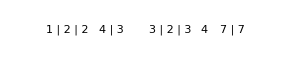

```mathematica
sosstart
```

```mathematica
sosinsidefirst:=Graphics[{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[{-1.3,-.5},{4.2,.5}],Black,Opacity[1],
listcar[{1,2,2,4,3},{0,0}],
listcar[{3,2,3,4,7,7},{2.6,0}]},PlotRange->{{-1.8,6},{-.65,.65}},
ImageSize->300]
```

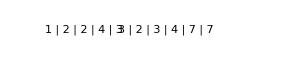

```mathematica
sosinsidefirst
```

```mathematica
sosoutsidefirst:=Graphics[{White,Opacity[0],EdgeForm[{Thick,Blue}],
Rectangle[{-1.7+.198,-.5},{5.8-.198,.5}],Black,Opacity[1],
listcar[{1,2,2},{-.8+.198,0}],listcar[{4,3},{.75+.198,0}],
listcar[{3,2,3},{2.7-.198,0}],listcar[{4},{4-.198,0}],
listcar[{7,7},{5-.198,0}]},PlotRange->{{-3,6},{-.65,.65}},
ImageSize->300]
```

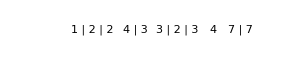

```mathematica
sosoutsidefirst
```

```mathematica
sosend:=Graphics[{Opacity[1],listcar[{1,2,2,4,3,3,2,3,4,7,7},{0,0}]},PlotRange->{{-3,6},{-.5,.5}},
ImageSize->300]
```

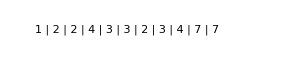

```mathematica
sosend
```

### Make diagram

```mathematica
alabel[name_,pos_]:=Text[Style[Framed[name],FontSize->12,FontFamily->"Arial"],Scaled[pos],Background->White]
```

```mathematica
myarr[pos1_,pos2_,setback_]:=Arrow[{Scaled[pos1],Scaled[pos2]},Scaled[setback]]
```

```mathematica
Remove[m1,c1]
```

```mathematica
m1="join inside first"
```

join inside first

join inside first

join inside first

«1 more identical outputs»

```mathematica
"join inside first"
```

join inside first

join inside first

join inside first

«1 more identical outputs»

```mathematica
m2="join outside first"
```

join outside first

join outside first

join outside first

«1 more identical outputs»

```mathematica
"join outside first"
```

join outside first

join outside first

join outside first

«1 more identical outputs»

```mathematica
m3="join"
```

join

join

join

«1 more identical outputs»

### The diagram

```mathematica
Graphics[
{Arrowheads[.03],,myarr[{0,0},{.5,1},.0012],myarr[{0,0},{.5,-1},.0012],myarr[{.5,1},{1,.15},.0012],myarr[{.5,-1},{1,-.15},.001],alabel[m1,.5({0,0}+{.5,1})],alabel[m2,.5({0,0}+{.5,-1})],alabel[m3 ,.5({.5,1}+{1,.15})],
alabel[m3,.5({.5,-1}+{1,-.15})],
Inset[sosstart,Scaled[{0,0}]],Inset[sosinsidefirst,Scaled[{.5,1}]],Inset[sosoutsidefirst,Scaled[{.42,-1}]],Inset[sosend,Scaled[{1,.15}]],Inset[sosend,Scaled[{1,-.15}]]
},
AspectRatio->.3,ImageSize->700
]
```

-Graphics-

-Graphics-